```mathematica
ClearAll["Global`*"]
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/elastic_obstacle/monolithic/solution/data.csv"]
```

```mathematica
t = Table[ToExpression[{t[[i,1]],t[[i,6]]}],{i,1,Length[t]}]
```

```mathematica
t={{1,0.5796076351345737},{2,0.5796078336155812},{3,0.5796086797477593},{4,0.5796102187133457},{5,0.5796123777986378},{6,0.5796150858659335},{7,0.5796183470431808},{8,0.5796222456864735},{9,0.5796268937589161},{10,0.5796323533707227},{11,0.5801505828943562},{12,0.5802737868850155},{13,0.5803943128053856},{14,0.5805909703704263},{15,0.5808423811170876},{16,0.5811211867016368},{17,0.5814047809059464},{18,0.5816795958922995},{19,0.5819432406877683},{20,0.5822030952138685},{21,0.5824719151163478},{22,0.5827625642784512},{23,0.5830841464949137},{24,0.5834406764838188},{25,0.5838318350079034},{26,0.5842543923484549},{27,0.584703073204396},{28,0.5851705670364674},{29,0.5856472163109281},{30,0.586121100108791},{31,0.5865788433769101},{32,0.5870069578071941},{33,0.5873932354888298},{34,0.5877277680092894},{35,0.5880034165352852},{36,0.5882158126468907},{37,0.5883630948334521},{38,0.5884455649427897},{39,0.5884653494776979},{40,0.588426059418506},{41,0.5883324111494133},{42,0.5881897982241577},{43,0.5880038521694274},{44,0.587780061941912},{45,0.58752351903411},{46,0.5872388245307937},{47,0.5869301526451542},{48,0.5866014282240948},{49,0.5862565527418843},{50,0.5858996078098337},{51,0.5855349767375261},{52,0.585167349715323},{53,0.584801610350429},{54,0.5844426320504164},{55,0.5840950336977389},{56,0.5837629498426857},{57,0.5834498610088533},{58,0.5831585094478895},{59,0.5828909024469631},{60,0.582648386389155},{61,0.5824317645318507},{62,0.5822414303366444},{63,0.5820774935642516},{64,0.5819398845070366},{65,0.5818284295716044},{66,0.5817428973567799},{67,0.5816830181897253},{68,0.581648482259389},{69,0.5816389225092742},{70,0.5816538885408009},{71,0.5816928169998146},{72,0.5817550024444534},{73,0.5818395709494784},{74,0.5819454572882958},{75,0.5820713859685256},{76,0.5822158568663827},{77,0.5823771374510882},{78,0.5825532649974288},{79,0.5827420630203334},{80,0.5829411758687368},{81,0.5831481238182544},{82,0.5833603784087011},{83,0.583575454888041},{84,0.583791016361152},{85,0.5840049834858072},{86,0.5842156449831177},{87,0.5844217682423757},{88,0.5846227161890892},{89,0.5848185869487509},{90,0.5850104084523641},{91,0.585200445669416},{92,0.5853927249867878},{93,0.5855939758039587},{94,0.5881075602821193},{95,0.5851787114740082},{96,0.5849454840434516},{97,0.5849670948174153},{98,0.5849560755253591},{99,0.5849025396411769},{100,0.5848155927820711}}
```

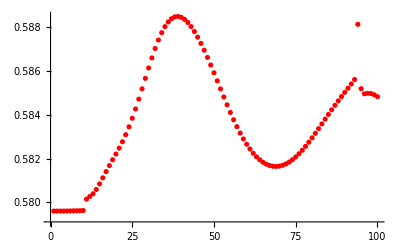

```mathematica
ListPlot[t,PlotStyle->Red]
```